# Discontinuous Galerkin

## Weak Formulation (Modal DG)

By Manuel A. Diaz, NTU, 2012.07.10

## Basis Function

```mathematica
legendreP =Table[LegendreP[i,𝒳],{i,0,6}];
Column[legendreP] // TraditionalForm
```

1
𝒳
1/2 (3 𝒳^2-1)
1/2 (5 𝒳^3-3 𝒳)
1/8 (35 𝒳^4-30 𝒳^2+3)
1/8 (63 𝒳^5-70 𝒳^3+15 𝒳)
1/16 (231 𝒳^6-315 𝒳^4+105 𝒳^2-5)

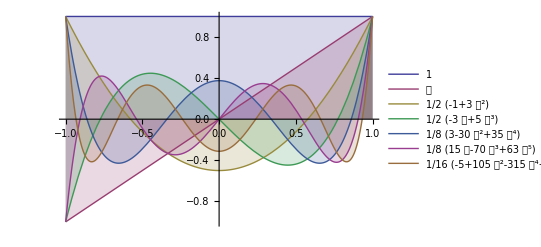

```mathematica
Plot[Evaluate[legendreP],{𝒳,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

## Normalization of Basis Functions

Define the size of our interval, I_j, as Δx_j. This interval and it will be identified by its middel point x_j. Notice that our basis polynomials work on the range of [-1,1]. thus we are now interested in finding a way to normalize them for interval  [-Δx/2,Δ/2].

The first idea to scale them is by making the change of variable 𝒳 → x-x_j, grand Schmidt ortogonalization process to build a new set or orthogonal polynomials.

### Initialize Notation

```mathematica
Quit[];
```

```mathematica
Needs["Notation`"]
```

based on http://en.wikipedia.org/wiki/Gram-Schmidt_process, we configure:

```mathematica
Notation[<a_[x_],b_[x_]> ⟹ Integrate[a_[x_] b_[x_],{x_,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
Notation[<a_,b_> ⟹ Integrate[a_ b_,{z,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

```mathematica
Notation[Subscript[proj, u_][v_] ⟹ (<u_,v_>)/(<u_,u_>)u_]
```

Testing:

```mathematica
<Subscript[v, 1][z],Subscript[v, 1][z]>
```

∫_(-Δx_j/2)^(Δx_j/2) v_1[z]^2 ⅆz

```mathematica
<a z,z>
```

(a Δx_j^3)/12

```mathematica
(<a[z],b[z]>)/(<a[z],a[z]>)a[z] == Subscript[proj, a[z]][b[z]]
```

True

```mathematica
Symbolize[Subscript[Δx, j]]; Symbolize[Subscript[x, j]];Symbolize[Subscript[I, j]];Symbolize[Subscript[v, _]];
```

### Building Scaled Legendre Polynomials using Gram Schmidt Orthogonalization process

#### Procedure 1: (not so good)

based on http : // en.wikipedia.org/wiki/Gram - Schmidt_process, we configure :

Defining our initial vectors,

```mathematica
Table[Subscript[v, i]=z^i,{i,0,6}](* here z = x-Subscript[x, j] *)
```

{1,z,z^2,z^3,z^4,z^5,z^6}

Compute initial projection

```mathematica
Subscript[u, 0]=Subscript[v, 0]
```

1

```mathematica
Subscript[u, 1]=Subscript[v, 1]-Subscript[proj, Subscript[u, 0]][Subscript[v, 1]]
```

z

```mathematica
scaledLegendre = Table[Subscript[u, i+1]=Subscript[v, i+1]-Subscript[proj, Subscript[u, i-1]][Subscript[v, i+1]] -Subscript[proj, Subscript[u, i]][Subscript[v, i+1]],{i,1,5}] ;
```

```mathematica
scaledLegendre /. z -> x-Subscript[x, j]//Column
```

(x-x_j)^2-Δx_j^2/12
(x-x_j)^3-3/20 (x-x_j) Δx_j^2
(x-x_j)^4-3/14 Δx_j^2 ((x-x_j)^2-Δx_j^2/12)
(x-x_j)^5-5/18 Δx_j^2 ((x-x_j)^3-3/20 (x-x_j) Δx_j^2)
(x-x_j)^6-(885 Δx_j^2 ((x-x_j)^4-3/14 Δx_j^2 ((x-x_j)^2-Δx_j^2/12)))/4444

#### Procedure 2: (way much better)

based on http : // mathworld.wolfram.com/Gram - SchmidtOrthonormalization.html, we configure :

```mathematica
Subscript[p, 0]=1;
Subscript[p, 1]=(z - (<z Subscript[p, 0],Subscript[p, 0]>)/(<Subscript[p, 0],Subscript[p, 0]>))Subscript[p, 0];
```

```mathematica
scaledLegendre=Table[Subscript[p, i+1]=(z - (<z Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i],Subscript[p, i]>))Subscript[p, i] -(<Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i-1],Subscript[p, i-1]>)Subscript[p, i-1] ,{i,1,6}]//Expand ;
```

```mathematica
Join[{Subscript[p, 0]},{Subscript[p, 1]},scaledLegendre] /.z-> x-Subscript[x, j]//Column
```

1
x-x_j
(x-x_j)^2-Δx_j^2/12
(x-x_j)^3-3/20 (x-x_j) Δx_j^2
(x-x_j)^4-3/14 (x-x_j)^2 Δx_j^2+(3 Δx_j^4)/560
(x-x_j)^5-5/18 (x-x_j)^3 Δx_j^2+5/336 (x-x_j) Δx_j^4
(x-x_j)^6-15/44 (x-x_j)^4 Δx_j^2+5/176 (x-x_j)^2 Δx_j^4-(5 Δx_j^6)/14784
(x-x_j)^7-21/52 (x-x_j)^5 Δx_j^2+(105 (x-x_j)^3 Δx_j^4)/2288-(35 (x-x_j) Δx_j^6)/27456

#### Comparing with mathematica internal function

```mathematica
scaledLegendre2 = Orthogonalize[{1,z,z^2,z^3,z^4,z^5,z^6},Integrate[#1 #2,{z,-Δx/2,Δx/2}]&] //Expand/.z-> x-Subscript[x, j] ;
```

```mathematica
scaledLegendre2 //Factor//Column
```

1/(√Δx)
(2 √3 z)/(√(Δx^3))
(√5 (12 z^2-Δx^2))/(2 √(Δx^5))
(√7 z (20 z^2-3 Δx^2))/(√(Δx^7))
(3 (560 z^4-120 z^2 Δx^2+3 Δx^4))/(8 √(Δx^9))
(√11 z (1008 z^4-280 z^2 Δx^2+15 Δx^4))/(4 √(Δx^11))
(√13 (14784 z^6-5040 z^4 Δx^2+420 z^2 Δx^4-5 Δx^6))/(16 √(Δx^13))

### Normalization Constants

```mathematica
coefficients = Table[Subscript[a, n,m]= (<Subscript[p, n],Subscript[p, m]>),{n,0,7},{m,0,7}];
```

```mathematica
coefficients // TableForm
```

Δx_j | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δx_j^3/12 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Δx_j^5/180 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Δx_j^7/2800 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Δx_j^9/44100 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Δx_j^11/698544 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Δx_j^13/11099088 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Δx_j^15/176679360

```mathematica
coef = Diagonal[coefficients]
```

{Δx_j,Δx_j^3/12,Δx_j^5/180,Δx_j^7/2800,Δx_j^9/44100,Δx_j^11/698544,Δx_j^13/11099088,Δx_j^15/176679360}

### Plot Scaled Legendre Polynomials

```mathematica
orthogonalpolinomials = Join[{Subscript[u, 0]},{Subscript[u, 1]},scaledLegendre]/. Subscript[Δx, j]->1;
```

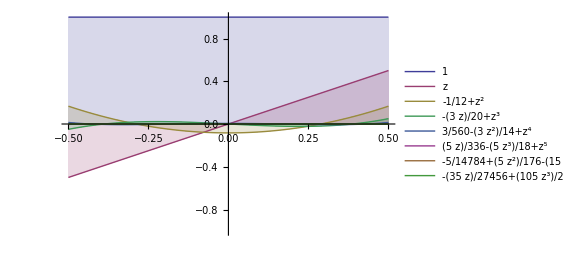

```mathematica
Plot[Evaluate[orthogonalpolinomials],{z,-0.5,0.5},Filling->Axis,PlotLegends->"Expressions",PlotRange->{-1,1}]
```

So having this scaled functions we can think on using them as basis functions to expand otherpolynomials just as we did in FEM,